Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 4 Euler method
Do 10 steps. Solve exactly. Compute the error.

1.  y'[x] + 0.2 y[x] == 0 ; y[0] == 5, h == 0.2

I don’t try to work out the Euler method. I’m only interested in what NDSolve can do, and its output compared with exact solutions, if they are available. (I should mention that problem 3 below succeeds in something I’ve been wanting to do.) About the text answers. All the DSolve solutions match text answers in this section, as marked with green cells. The text answers also contain information about numerical errors expected when the method in focus is applied. However, since I don’t apply the text’s methods, I naturally skipped concentrating on those numerical errors.

```mathematica
Clear["global`*"]
```

This is trying out the exact solution in order to compare it with the numerical solution. First the exact solution.

```mathematica
s1=DSolve[{y'[x]+0.2 y[x]==0,y[0]==5},y,{x,0,30}]
```

{{y→Function[{x},5. ⅇ^(-0.2 x)]}}

And a table and plot showing exact function values.

```mathematica
jq=Table[y[x]/.s1,{x,0,5,0.5}];
p1=Plot[5. ⅇ^(-0.2 x),{x,0,5},PlotStyle->{Red,Thickness[0.008]}];
```

Then an interpolating function.

```mathematica
s2=NDSolve[{y'[x]+0.2 y[x]==0,y[0]==5},y,{x,0,5}]
```

{{y→InterpolatingFunction[{{0., 5.}}, <>]}}

And a table showing interpolated values.

```mathematica
jr=Table[y[x]/.s2,{x,0,5,0.5}];
```

Then a two-column table showing the difference between exact and interpolated. It looks like the two tables agree to S7.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,0,5,0.5}]]
```

{{5.00000000},{5.00000000}}
{{4.52418710},{4.52418720}}
{{4.09365380},{4.09365350}}
{{3.70409110},{3.70409110}}
{{3.35160020},{3.35160010}}
{{3.03265330},{3.03265330}}
{{2.74405820},{2.74405810}}
{{2.48292650},{2.48292650}}
{{2.24664480},{2.24664480}}
{{2.03284830},{2.03284830}}
{{1.83939720},{1.83939720}}

And finally a look at the plot of the two functions.

```mathematica
p2=Plot[Evaluate[y[x]/.s2],{x,0,5}, PlotStyle->{White,Thickness[0.004]}];
```

The two solutions track pretty well. Exact solution is red.

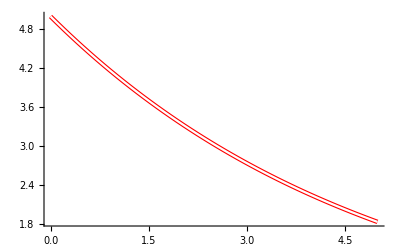

```mathematica
Show[p1,p2]
```

3.  y'[x]==(y[x]-x)^2 ; y[0]==0, h==0.1

```mathematica
Clear["global`*"]
```

Here I will do something a little different. First the exact solution, which I find still works for this problem.

```mathematica
s1=DSolve[{y'[x]==(y[x]-x)^2 , y[0]==0},y[x],x]
```

{{y[x]→(1-ⅇ^(2 x)+x+ⅇ^(2 x) x)/(1+ⅇ^(2 x))}}

```mathematica
Simplify[ExpToTrig[(1-ⅇ^(2 x)+x+ⅇ^(2 x) x)/(1+ⅇ^(2 x))]]
```

x-Tanh[x]

And a plot of the exact solution, for purple background trace.

```mathematica
p1=Plot[(1-ⅇ^(2 x)+x+ⅇ^(2 x) x)/(1+ⅇ^(2 x)),{x,0,5},PlotStyle->{RGBColor[0.7,0.3,0.7],Thickness[0.008]}];
```

Then the interpolated solution using NDSolve.

```mathematica
s2=NDSolve[{y'[x]==(y[x]-x)^2 , y[0]==0},y,{x,0,5}]
```

{{y→InterpolatingFunction[{{0., 5.}}, <>]}}

Then a table of values derived from the interpolated solution.

```mathematica
jr=Table[y[x]/.s2,{x,0,5,0.005}];
jrf = Flatten[jr];
lx=Range[0,5,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

And the plot of the exact solution overlaid by the plot of points from the interpolating function of NDSolve.

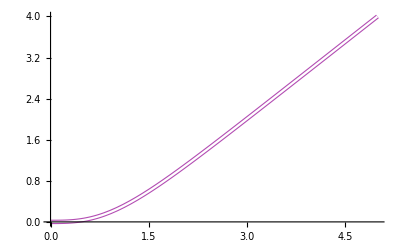

```mathematica
Show[p1,p3]
```

But what if I want an actual equation to represent the numerical solution? With a little experimentation I find the interval for 26 points, which is not too demanding of space or cpu.

```mathematica
jrs=Table[y[x]/.s2,{x,0,5,0.2}]
jrfs=Flatten[jrs];
```

{{0.},{0.00262467},{0.020051},{0.0629505},{0.135963},{0.238406},{0.366345},{0.514648},{0.678331},{0.853194},{1.03597},{1.22426},{1.41633},{1.61097},{1.80737},{2.00495},{2.20332},{2.40223},{2.60149},{2.801},{3.00067},{3.20045},{3.4003},{3.6002},{3.80014},{4.00009}}

And providing for my 26 domain points.

```mathematica
lxs=Range[0,5,0.2];
thrs=Thread[{lxs,jrfs}]
```

{{0.,0.},{0.2,0.00262467},{0.4,0.020051},{0.6,0.0629505},{0.8,0.135963},{1.,0.238406},{1.2,0.366345},{1.4,0.514648},{1.6,0.678331},{1.8,0.853194},{2.,1.03597},{2.2,1.22426},{2.4,1.41633},{2.6,1.61097},{2.8,1.80737},{3.,2.00495},{3.2,2.20332},{3.4,2.40223},{3.6,2.60149},{3.8,2.801},{4.,3.00067},{4.2,3.20045},{4.4,3.4003},{4.6,3.6002},{4.8,3.80014},{5.,4.00009}}

The idea being that I don’t want to plot points this time, or an interpolated function, I want a real equation. I can use the set of points to call for an interpolating polynomial.

```mathematica
ipt=Simplify[InterpolatingPolynomial[thrs,x]]
```

0.+0.0261475 x-0.478785 x^2+4.19826 x^3-18.5659 x^4+60.0462 x^5-141.127 x^6+250.286 x^7-345.692 x^8+380.094 x^9-337.866 x^10+245.503 x^11-146.97 x^12+72.8641 x^13-30.001 x^14+10.2647 x^15-2.91337 x^16+0.682995 x^17-0.131291 x^18+0.0204636 x^19-0.00254374 x^20+0.000246076 x^21-0.0000178439 x^22+9.12057×10^-7 x^23-2.92899×10^-8 x^24+4.44369×10^-10 x^25

And with one copy and paste, my Pinnochio IP becomes a real equation.

```mathematica
pt[x_]=0.+0.02614749772157321 x-0.47878452095496377 x^2+4.198262542436343 x^3-18.565885975456638 x^4+60.04624852508333 x^5-141.12670386028825 x^6+250.28565670824995 x^7-345.6917160584147 x^8+380.09424848385635 x^9-337.86585361013624 x^10+245.50275327522917 x^11-146.9702428483498 x^12+72.86407583833704 x^13-30.001012857996283 x^14+10.264725913159012 x^15-2.9133662891118424 x^16+0.6829951452560038 x^17-0.13129100464415203 x^18+0.020463577227472583 x^19-0.0025437384096592065 x^20+0.0002460759857445973 x^21-0.00001784389593520076 x^22+9.120572579204695*^-7 x^23-2.928991207288055*^-8 x^24+4.4436905900150525*^-10 x^25
```

0.+0.0261475 x-0.478785 x^2+4.19826 x^3-18.5659 x^4+60.0462 x^5-141.127 x^6+250.286 x^7-345.692 x^8+380.094 x^9-337.866 x^10+245.503 x^11-146.97 x^12+72.8641 x^13-30.001 x^14+10.2647 x^15-2.91337 x^16+0.682995 x^17-0.131291 x^18+0.0204636 x^19-0.00254374 x^20+0.000246076 x^21-0.0000178439 x^22+9.12057×10^-7 x^23-2.92899×10^-8 x^24+4.44369×10^-10 x^25

```mathematica
p4=Plot[pt[x],{x,0,5},PlotStyle->{White,Thickness[0.004]}];
```

Now to see how the polynomial equation compares to the exact formula.

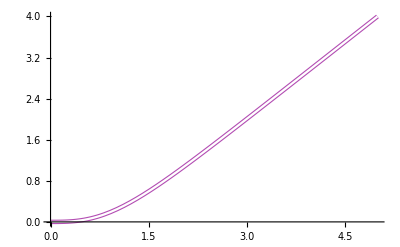

```mathematica
Show[p1,p4]
```

The table below shows 5S minimum from a poly of order 25. Since the underlying functions for problems 1 and 3 are similar, it looks like I may have cost myself 1 or 2 significant figures of accuracy by making an equation out of interpolated points. Using the enhancement options appearing in problem 9 and following, I could probably regain these lost decimals, and maybe more.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,pt[x]},{8,8}],{x,0,5,0.5}]]
```

{{0.00000000},0.00000000}
{{0.03788284},0.03788592}
{{0.23840584},0.23840586}
{{0.59485175},0.59485169}
{{1.03597240},1.03597240}
{{1.51338570},1.51338570}
{{2.00494520},2.00494520}
{{2.50182210},2.50182230}
{{3.00067070},3.00067090}
{{3.50024680},3.50023560}
{{4.00009080},4.00005340}

5 - 10 Improved Euler method
Do 10 steps. Solve exactly. Compute the error.

5.  y'[x] == y; y[0] == 1, h == 0.1

```mathematica
Clear["Global`*"]
```

Good luck to the improved Euler method, whatever it is. I am sticking with NDSolve. Though first to appear, as usual, is the exact equation with DSolve.

```mathematica
s1=DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

And a plot of the exact solution, for brown background trace. (Plot retracted.)

```mathematica
p1=Plot[ⅇ^x,{x,0,5},PlotStyle->{Brown,Thickness[0.008]}];
```

Then the interpolated solution using NDSolve.

```mathematica
s2=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,5}]
```

{{y→InterpolatingFunction[{{0., 5.}}, <>]}}

I realize that for what I am doing in this problem the following table of sample points is not necessary. Still, I prefer to do it that way for now.

```mathematica
jr=Table[y[x]/.s2,{x,0,5,0.005}];
jrf = Flatten[jr];
lx=Range[0,5,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

And the plot of the exact solution overlaid by the plot of points from the interpolating function of NDSolve.

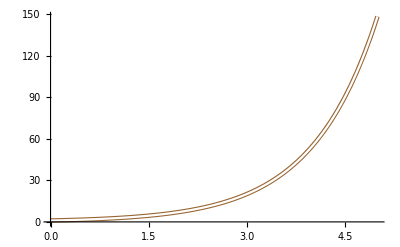

```mathematica
Show[p1,p3]
```

Now, a table comparison of output. Note that the points from both compared functions are being cooked up on the fly. I think there is agreement to 6S.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,0,5,0.5}]]
```

{{1.00000000},{1.00000000}}
{{1.64872130},{1.64872120}}
{{2.71828180},{2.71828160}}
{{4.48168910},{4.48168570}}
{{7.38905610},{7.38905210}}
{{12.18249400},{12.18249500}}
{{20.08553700},{20.08552100}}
{{33.11545200},{33.11540600}}
{{54.59815000},{54.59810600}}
{{90.01713100},{90.01713800}}
{{148.41316000},{148.41317000}}

7.  y'[x]-x y[x]^2==0 ; y[0]==1, h==0.1

Here’s another one.

```mathematica
Clear["Global`*"]
```

```mathematica
s1=DSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y[x],x]
```

{{y[x]→-2/(-2+x^2)}}

The text answer is in a slightly different format, so I had better check the following.

```mathematica
PossibleZeroQ[(-2/(-2+x^2))-1/(1-x^2/2)]
```

True

Luckily I can still acquire an exact solution from DSolve. And a plot of the exact solution, for green background trace.

```mathematica
p1=Plot[-2/(-2+x^2),{x,0,1.2},PlotStyle->{RGBColor[0.2,0.8,0.2],Thickness[0.008]}];
```

Then the interpolated solution using NDSolve.

```mathematica
s2=NDSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y,{x,0,1.2}]
```

{{y→InterpolatingFunction[{{0., 1.2}}, <>]}}

I’m still going with the list of sample points.

```mathematica
jr=Table[y[x]/.s2,{x,0,1.2,0.005}];
jrf = Flatten[jr];
lx=Range[0,1.2,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

Until I restricted the domain to avoid asymptotes, I got a lot of warning messages. I’ll try plotting the exact solution overlaid by the plot of points from the interpolating function of NDSolve.

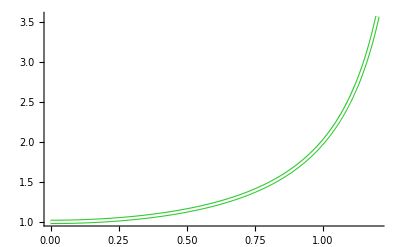

```mathematica
Show[p1,p3]
```

In comparing the functions’s values in the following table, I see that the accuracy falls off from 7S at the top of the table to only 5S at the bottom

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,0,1.2,0.1}]]
```

{{1.00000000},{1.00000000}}
{{1.00502510},{1.00502520}}
{{1.02040820},{1.02040830}}
{{1.04712040},{1.04712050}}
{{1.08695650},{1.08695670}}
{{1.14285710},{1.14285730}}
{{1.21951220},{1.21951240}}
{{1.32450330},{1.32450340}}
{{1.47058820},{1.47058870}}
{{1.68067230},{1.68067290}}
{{2.00000000},{2.00000110}}
{{2.53164560},{2.53164710}}
{{3.57142860},{3.57143280}}

9.  Do problem 7 using Euler’s method with h = 0.1 and compare the accuracy.

Since the problem instructions don’t relate well to my side-stepping path through the section, I will substitute an experiment in tightening agreement between exact and interpolated results, for the previous problem.

```mathematica
s3=NDSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y,{x,0,1.2},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]
```

{{y→InterpolatingFunction[{{0, 1.1999999999999999555910790149937384}}, <>]}}

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s3},{10,10}],{x,0,1.2,0.1}]]
```

{{1.0000000000},{1.0000000000}}
{{1.0050251260},{1.0050251260}}
{{1.0204081630},{1.0204081630}}
{{1.0471204190},{1.0471204190}}
{{1.0869565220},{1.0869565220}}
{{1.1428571430},{1.1428571430}}
{{1.2195121950},{1.2195121950}}
{{1.3245033110},{1.3245033110}}
{{1.4705882350},{1.4705882350}}
{{1.6806722690},{1.6806722690}}
{{2.0000000000},{2.0000000000}}
{{2.5316455700},{2.5316455700}}
{{3.5714285710},{3.5714285710}}

The above table is sort of amazing, presenting as it does, 11S with no noticeable increase in execution time.

11 - 17 Classical Runge-Kutta method of fourth order
Do 10 steps. Compare as indicated.

11.  y'[x]-x y[x]^2==0 ; y[0]==1, h==0.1. Compare with problem 7. Apply the error estimate (10) to y_10.

Mention of Runga-Kutta must be acknowledged. Seems like I worked with this in the old days, and have to give it a spin at least.

```mathematica
Clear["Global`*"]
```

DSolve is still working, a nice convenience. The green cell below is equivalent to the text answer, see problem 7 for reconciliation.

```mathematica
s1=DSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y[x],x]
```

{{y[x]→-2/(-2+x^2)}}

The tan background plot is the exact one. I have to keep the domain small for this one too, because of pesky asymptotes.

```mathematica
p1=Plot[-2/(-2+x^2),{x,0,1.2},PlotStyle->{RGBColor[0.85,0.7,0.2],Thickness[0.008]}];
```

The interpolating function from NDSolve comes next. Here I tried to do max steps → 10, but that only took me out to x = 0.19, so I increased them.

```mathematica
s2=NDSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y,{x,0,1.2},Method->"ExplicitRungeKutta",MaxSteps->20]
```

{{y→InterpolatingFunction[{{0., 1.2}}, <>]}}

And then the set of points for overlaying.

```mathematica
jr=Table[y[x]/.s2,{x,0,1.2,0.005}];
jrf = Flatten[jr];
lx=Range[0,1.2,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

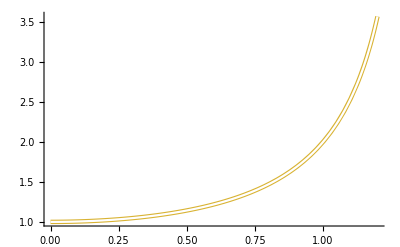

```mathematica
Show[p1,p3]
```

With the restricted number of steps, it looks like I get 4S minimum.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,0,1.2,0.1}]]
```

{{1.00000000},{1.00000000}}
{{1.00502510},{1.00502500}}
{{1.02040820},{1.02040810}}
{{1.04712040},{1.04712040}}
{{1.08695650},{1.08695410}}
{{1.14285710},{1.14284640}}
{{1.21951220},{1.21948600}}
{{1.32450330},{1.32445870}}
{{1.47058820},{1.47054440}}
{{1.68067230},{1.68067230}}
{{2.00000000},{1.99984180}}
{{2.53164560},{2.53154950}}
{{3.57142860},{3.57142860}}

Below I find that increasing the MaxSteps does not help the accuracy.

```mathematica
s3=NDSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y,{x,0,1.2},Method->"ExplicitRungeKutta",MaxSteps->2000]
```

{{y→InterpolatingFunction[{{0., 1.2}}, <>]}}

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s3},{8,8}],{x,0,1.2,0.1}]]
```

{{1.00000000},{1.00000000}}
{{1.00502510},{1.00502500}}
{{1.02040820},{1.02040810}}
{{1.04712040},{1.04712040}}
{{1.08695650},{1.08695410}}
{{1.14285710},{1.14284640}}
{{1.21951220},{1.21948600}}
{{1.32450330},{1.32445870}}
{{1.47058820},{1.47054440}}
{{1.68067230},{1.68067230}}
{{2.00000000},{1.99984180}}
{{2.53164560},{2.53154950}}
{{3.57142860},{3.57142860}}

But tuning up the Goals and WorkingPrecision works well.

```mathematica
s4=NDSolve[{y'[x]-x y[x]^2==0 , y[0]==1},y,{x,0,1.2},Method->"ExplicitRungeKutta",AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]
```

{{y→InterpolatingFunction[{{0, 1.1999999999999999555910790149937384}}, <>]}}

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s4},{8,8}],{x,0,1.2,0.1}]]
```

{{1.00000000},{1.00000000}}
{{1.00502510},{1.00502510}}
{{1.02040820},{1.02040820}}
{{1.04712040},{1.04712040}}
{{1.08695650},{1.08695650}}
{{1.14285710},{1.14285710}}
{{1.21951220},{1.21951220}}
{{1.32450330},{1.32450330}}
{{1.47058820},{1.47058820}}
{{1.68067230},{1.68067230}}
{{2.00000000},{2.00000000}}
{{2.53164560},{2.53164560}}
{{3.57142860},{3.57142860}}

13.  y'[x]==1+y[x]^2; y[0]==0, h==0.1

```mathematica
Clear["Global`*"]
```

I think Runga-Kutta is good if I have to work with paper and pencil or generic software, but with Mathematica it’s sort of irrelevant. With the present problem I see that DSolve is giving me caveats, but it’s still putting out an answer.

```mathematica
s1=DSolve[{y'[x]==1+y[x]^2, y[0]==0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Tan[x]}}

The background plot is the exact one, a teal-ish hue. Here there are more asymptotes to dodge.

```mathematica
p1=Plot[Tan[x],{x,0,1.2},PlotStyle->{RGBColor[0.2,0.5,0.7],Thickness[0.008]}];
```

Next comes the NDSolve interpolating function. I’m dropping reference to Runga-Kutta in the formulation for NDSolve, but putting in the accuracy enhancers.

```mathematica
s2=NDSolve[{y'[x]==1+y[x]^2, y[0]==0},y,{x,0,1.2},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]
```

{{y→InterpolatingFunction[{{0, 1.1999999999999999555910790149937384}}, <>]}}

Next the overlay points are provided.

```mathematica
jr=Table[y[x]/.s2,{x,0,1.2,0.005}];
jrf = Flatten[jr];
lx=Range[0,1.2,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

Just before the overlay plot.

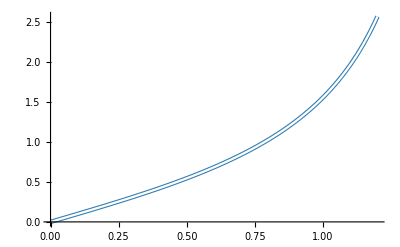

```mathematica
Show[p1,p3]
```

And the satisfying table.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,0,1.2,0.1}]]
```

{{0.00000000},{0.00000000}}
{{0.10033467},{0.10033467}}
{{0.20271004},{0.20271004}}
{{0.30933625},{0.30933625}}
{{0.42279322},{0.42279322}}
{{0.54630249},{0.54630249}}
{{0.68413681},{0.68413681}}
{{0.84228838},{0.84228838}}
{{1.02963860},{1.02963860}}
{{1.26015820},{1.26015820}}
{{1.55740770},{1.55740770}}
{{1.96475970},{1.96475970}}
{{2.57215160},{2.57215160}}

15.  y'[x] + y[x] Tan[x] == Sin[2 x] ; y[0] == 1, h == 0.1

```mathematica
Clear["Global`*"]
```

Looks like there are two trig factors in this one.

```mathematica
s1=DSolve[{y'[x]+y[x] Tan[x]==Sin[2 x],y[0]==1},y[x],x]
```

{{y[x]→3 Cos[x]-2 Cos[x]^2}}

The background plot is the exact one, orange hue. With this one I can extend the plot domain a bit.

```mathematica
p1=Plot[3 Cos[x]-2 Cos[x]^2,{x,0,5},PlotStyle->{Orange,Thickness[0.008]}];
```

Now for the NDSolve interpolating function. By now the accuracy enhancers are routine additions. In this particular problem I notice that there must be some kind of obstruction which NDSolve in encountering, because s2 is complaining if I try to raise the x limitation.

```mathematica
s2=NDSolve[{y'[x]+y[x] Tan[x]==Sin[2 x],y[0]==1},y,{x,0,1.56},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]
```

{{y→InterpolatingFunction[{{0, 1.5600000000000000532907051820075139}}, <>]}}

Next come the overlay points. But I find the overlay points are restricted to the smaller x-interval.

```mathematica
jr=Table[y[x]/.s2,{x,0,1.56,0.005}];
jrf = Flatten[jr];
lx=Range[0,1.56,0.005];
thr=Thread[{lx,jrf}];
p3=ListLinePlot[thr,PlotStyle->{White,Thickness[0.004]}];
```

So this time the overlay plot looks quite undermined because of the limited x-interval.

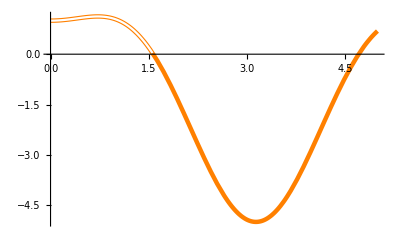

```mathematica
Show[p1,p3]
```

The interpolating function of NDSolve can’t go through the x-axis for some reason. I don’t understand why there should be a problem.

```mathematica
FindRoot[3 Cos[x]-2 Cos[x]^2,{x,1.5}]
```

{x→1.5708}

```mathematica
1.5707963267948966
```

This seems a little odd. The error messages give me a hint that a stiff system might be present, so I try specifying the Method. “Automatic” does not work, but “BDF” does. I find that I have to compromise on the accuracy enhancers to make it work.

```mathematica
s3=NDSolve[{y'[x]+y[x] Tan[x]==Sin[2 x],y[0]==1},y,{x,0,5},Method->"BDF",AccuracyGoal->11,PrecisionGoal->11,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{0, 5.0000000000000000000}}, <>]}}

I think it is time to drop the overlay of a list of sample points, it really isn’t necessary to do it that way. It was necessary in problem 3, in order to get an interpolating polynomial. But the NDSolve interpolating function can overlay on its own.

```mathematica
p4=Plot[y[x]/.s3,{x,0,5},PlotStyle->{White,Thickness[0.004]}];
```

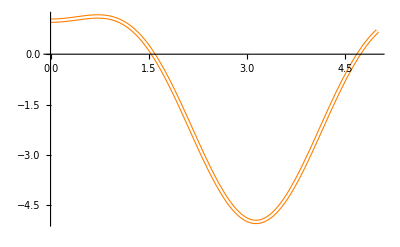

```mathematica
Show[p1,p4]
```

Despite the need to compromise a bit on Goals and WP, the table seems to still have 9S.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s3},{8,8}],{x,0,5,0.4}]]
```

{{1.00000000},{1.00000000}}
{{1.06647630},{1.06647630}}
{{1.11931970},{1.11931970}}
{{0.82446698},{0.82446698}}
{{-0.08930379},{-0.08930379}}
{{-1.59479690},{-1.59479690}}
{{-3.29968010},{-3.29968010}}
{{-4.60223290},{-4.60223290}}
{{-4.98806920},{-4.98806920}}
{{-4.29862660},{-4.29862660}}
{{-2.81543080},{-2.81543080}}
{{-1.11090560},{-1.11090560}}
{{0.24718481},{0.24718481}}

17.  y'[x]==4 x^3 y^2 ; y[0]==0.5, h==0.1

```mathematica
Clear["Global`*"]
```

Back to looking at a pure poly. Note: the text answers identifies the green cell below as y' instead of y, but I assume it is a typo on the text’s part.

```mathematica
s1=DSolve[{y'[x]==4 x^3 y[x]^2 , y[0]==0.5},y[x],x]
```

{{y[x]→-1./(-2.+x^4)}}

The plot shows the solution function to be as asymptote-prone as a tangent.

```mathematica
p1=Plot[y[x]/.s1,{x,-1,1},PlotStyle->{RGBColor[1,0.6,0.6],Thickness[0.008]}];
```

From the behavior of NDSolve, this problem function is not stiff. Mathematica gives me the message that the requested enhancement group can’t be realized, but I leave it in anyway.

```mathematica
s2=NDSolve[{y'[x]==4 x^3 y[x]^2 , y[0]==0.5},y,{x,-1,1},AccuracyGoal->∞,PrecisionGoal->10,WorkingPrecision->15]
```

NDSolve::precw: The precision of the differential equation ({{y'[x]==4 x^3 y[x]^2,y[0]==0.5},{},{},{},{}}) is less than WorkingPrecision (15.).

{{y→InterpolatingFunction[{{-1.00000000000000, 1.00000000000000}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1,1},PlotStyle->{White,Thickness[0.004]}];
```

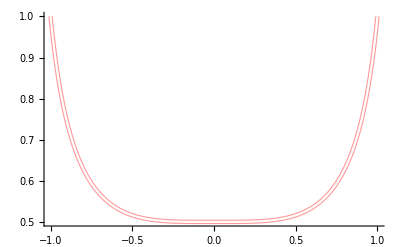

```mathematica
Show[p1,p2]
```

I’ve set the enhancers according to some pointers I picked up at SEMma, https://mathematica.stackexchange.com/questions/88042/precision-and-accuracy-in-ndsolve-and-nminimize, but it looks like 6S is the best I’m going to do with this one.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1,1,0.2}]]
```

{{1.00000000},{1.00000000}}
{{0.62877264},{0.62877262}}
{{0.53464500},{0.53464499}}
{{0.50648298},{0.50648298}}
{{0.50040032},{0.50040032}}
{{0.50000000},{0.50000000}}
{{0.50040032},{0.50040032}}
{{0.50648298},{0.50648298}}
{{0.53464500},{0.53464499}}
{{0.62877264},{0.62877262}}
{{1.00000000},{1.00000000}}

19.  CAS experiment. Euler-Cauchy vs. RK.
Consider the initial value problem

(17)  y'[x]==(y[x]-0.01 x^2)^2 Sin[x^2]+0.02 x ; y[0]==0.4  (solution: y ==1/[2.5 - S[x]]+0.01 x^2, where S[x] is the Fresnel integral (38) in appendix 3.1). (a) Solve (17) by Euler, improved Euler, and RK methods for 0 ≤ x ≤ 5 with step h = 0.2. Compare the errors for x = 1, 3, 5 and comment. (b) Graph solution curves of the ODE in (17) for various positive and negative initial values. (c) Do a similar experiment as in (a) for an initial value problem that has a monotone increasing or monotone decreasing solution. Compare the behavior of the error with that in (a). Comment.

```mathematica
Clear["Global`*"]
```

This one does seem to have a more complicated solution than previous problems, I’ll give it that. Otherwise, I treat it as just another problem, in spite of its wordy introduction. I found that by adding the Simplify command in the s1 equation below, I could get rid of some phantom imaginary elements which would have crept back in later.

```mathematica
s1=Simplify[DSolve[{y'[x]==(y[x]-0.01 x^2)^2 Sin[x^2]+0.02 x , y[0]==0.4},y[x],x]]
```

{{y[x]→(0.797885+0.0199471 x^2-0.01 x^2 FresnelS[√(2/π) x])/(1.99471-1. FresnelS[√(2/π) x])}}

```mathematica
k[x_]=(0.7978845608028654+0.019947114020071637 x^2-0.01 x^2 FresnelS[√(2/π) x])/(1.9947114020071637-1. FresnelS[√(2/π) x]);
```

The following is as close as I’m going to get to checking the solution.

```mathematica
k[0]
```

0.4

The background plot will have the exact solution in light blue.

```mathematica
p1=Plot[y[x]/.s1,{x,-1,1},PlotStyle->{RGBColor[0.6,0.6,1],Thickness[0.008]}];
```

NDSolve does not balk at solving the equation, though it does warn of a reduced precision compared with the requested level.

```mathematica
s2=NDSolve[{y'[x]==(y[x]-0.01 x^2)^2 Sin[x^2]+0.02 x , y[0]==0.4},y,{x,-1,1},AccuracyGoal->∞,PrecisionGoal->10,WorkingPrecision->15]
```

NDSolve::precw: The precision of the differential equation ({{y'[x]==0.02 x+Sin[x^2] (Times[«2»]+y[«1»])^2,y[0]==0.4},{},{},{},{}}) is less than WorkingPrecision (15.).

{{y→InterpolatingFunction[{{-1.00000000000000, 1.00000000000000}}, <>]}}

```mathematica
p2=Plot[y[x]/.s2,{x,-1,1},PlotStyle->{White,Thickness[0.004]}];
```

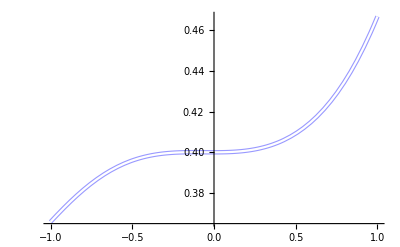

```mathematica
Show[p1,p2]
```

In spite of Mathematica saying that the precision would be inadequate, it looks great to me.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-1,1,0.2}]]
```

{{0.36583791},{0.36583791}}
{{0.38153063},{0.38153063}}
{{0.39250285},{0.39250285}}
{{0.39822168},{0.39822168}}
{{0.39997384},{0.39997384}}
{{0.40000000},{0.40000000}}
{{0.40082707},{0.40082707}}
{{0.40503637},{0.40503637}}
{{0.41534905},{0.41534905}}
{{0.43480094},{0.43480094}}
{{0.46667695},{0.46667695}}